```mathematica
f[x_]=1/((1+x^2)^(4/3))
```

1/((1+x^2)^(4/3))

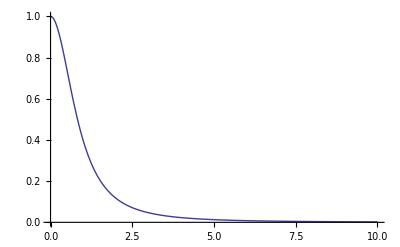

```mathematica
Plot[f[x], {x, 0, 10},PlotRange->Full]
```

```mathematica
Solve[t==1/(1+x),x]
```

{{x→(1-t)/t}}

```mathematica
D[(1-t)/t,t]
```

-(1-t)/t^2-1/t

```mathematica
D[1/(x+1),x]
```

-1/(1+x)^2

```mathematica
f2[t_]=((1+((1-t)/t)^2)^(-4/3+2))
```

(1+(1-t)^2/t^2)^(2/3)

```mathematica
Integrate[f2[x],{x,0,1}]
```

Integrate::idiv: Integral of (2 + 1/x^2 - 2/x)^2/3 does not converge on {0, 1}.

∫_0^1 (1+(1-x)^2/x^2)^(2/3)ⅆx